```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
mats = (#-1/($N)Tr[#]IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1, $N], $K*100000];
```

```mathematica
x = Partition[mats, $K];
```

```mathematica
x//Dimensions
```

{100000,9,9,9}

```mathematica
pot[y_] := 
-1/2 Sum[Tr[y[[i]].y[[j]].y[[i]].y[[j]]-y[[i]].y[[j]].y[[j]].y[[i]]], {i, 1, $K}, {j, 1, $K}];
```

```mathematica
V = Monitor[Table[pot[x[[k]]], {k, 1, Length[x]}], ProgressIndicator[(k-1)/(Length[x]-1)]];
```

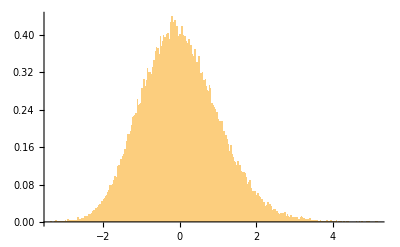

```mathematica
Histogram[Standardize[V//Chop], 400, PDF]
```